## All the data I need

What all this stuff is in words:
	
BulkStats:  A file with various measures over all people and all movies, discussed below

PeopleByMovies:  480k files inverting the original MoviesByPeople format to group
	 reviews by each reviewer instaef of grouping reviewers by movie.  Actually an augmented 
	 duplicate of TestFolder. Each element in each file gives {personid, movieid, score, date}
	peopleids:  Each of the 480k people has an id number.  Here they are in ascending order
	These files are concatenated and need to be read with ReadList.
	
probe:  A movie id and the ids of the people who reviewed it, but not the score, in ragged matrix format.  
	Getting the scores was left as an exercise to the reader who is supposed to go rummage after it.  The probe is a 
	subset of the training set where they "give you the answers"  so you can test one's algorithm.
	
probescores:  A synthesized dataset  giving the scores and dates belonging to each  
	review in "probe" {movieid, personid, score, date}
	
probesorted:  A sorted version of probe for the purpose of algorithm testing, low to 
	high personid  {movieid, personid, score, date}
	
probesortsample:  A small sample of probesorted, 2500 elements, for algorithm 
	testing  {movieid, personid, score, date}
	
synqual:  A Mathematica version of the qualifying dataset:  Gives {movie, reviewer, date}.  
	This is what one predicts from for the NetFlix prize.  About 1M elements.
	
TestFolder: 480k+ Mathematica files of all the movie reviews with {movieid, score, date} 
	headed by reviewer id in the filename. Same info, different format as PeopleByMovies  
	
titles:  Data of the form {movieid, year, name}

TrainingMma:  A folder with all of the original  data used to train the algorithm translated 
	into Mathematica readable format.  Also known by inversion as MoviesByPeople.  
	Each element in each file (named by movie) gives {personid, score, date}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

{answer,answer1.txt,answer1.txt.gz,answer2.txt.gz,answer3.txt.gz,answer4.txt,answer4.txt.gz,answer6.txt,answer6.txt.gz,answer7.txt.gz,answer8.txt.gz,answer9.txt.gz,BulkStats,.DS_Store,finalform,finalpairs,flubnanlist,fullknesset,mfanswer5.txt,mfanswer5.txt.gz,mfanswerclip2.txt.gz,mfanswerclip.txt,mfanswer.txt.gz,mfnonscram,mfnonscramscores,PeopleByMovies,peopleids,peopleids2,probe,probefinalscores,proberawscorelist,probescores,probesorted,probesortsample,pss2,qualNaNlist,qualnanpairs,qualsortnanpairs,rawsortsynscores,rawsynscores,sfasort,sortflubnanpos,sortnanlist,sortsyn,sortsyneval,sortsynfinalscores,sortsynflubnanfinalscores,straightsortfinalform,straightsortfinalpairs,synfinalscores,synqual,synqual2,synqualeval,synqualgf,synqualorderedpairs,synqualsort,TestFolder,titles,TrainingMma}

```mathematica
(*synqualsort=<<synqualsort;
Print["Dim[synqualsort] = ", Dimensions[synqualsort]]*)
(*probe=<<probe;
Print["Dim[probe] = ", Dimensions[probe]]
titles=<<titles;
Print["Dim[titles] = ",Dimensions[titles]]*)
people=<<peopleids;
Print["Dim[people] = ",Dimensions[people]]
(*probescores=<<probescores;
Print["Dim[probescores] = ",Dimensions[probescores]]*)
(*pss2=<<pss2;
Print["Dim[pss2] = ",Dimensions[pss2]]*)
```

Dim[people] = {480183}

```mathematica
probesorted=<<probesorted;
Print["Dim[probesorted] = ", Dimensions[probesorted]]
```

Dim[probesorted] = {1408395,4}

```mathematica
(*pss=<<probesortsample;
Print["Dim[probesortsample] = ",Dimensions[pss]]*)
```

Dim[people] = {480183}

```mathematica
synqualeval=<<synqualeval;
```

```mathematica
synqual=<<synqual;
```

```mathematica
Take[synqual,10]
```

{{1:,1046323,3274},{1:,1080030,3278},{1:,1830096,2994},{1:,368059,3067},{1:,802003,3232},{1:,513509,3106},{1:,1086137,3185},{1:,428698,3275},{1:,515850,3252},{1:,131974,3270}}

```mathematica
peoplefilenames=Table[StringJoin["personfile",ToString[people[[i]]]],{i,Length[people]}];
```

This is the old unmodified reversepersontable.  The new one (saved) incorporates the proper mapping of the six ghost people to the people in line just before them.

```mathematica
(*reversepersontable=Table[0,{2649429}];
Do[reversepersontable[[people[[i]]]]=i,{i,Length[people]}]*)
```

```mathematica
synqual=<<synqual;
```

```mathematica
Print["Dim[synqual] = ", Dimensions[synqual]]
synqual2=Table[{ToExpression[StringDrop[synqual[[i,1]],-1]],synqual[[i,2]],i},{i,Length[synqual]}];
```

Dim[synqual] = {2817131,3}

```mathematica
synqualsort=Sort[synqual2,#2[[2]]>#1[[2]]&];
```

```mathematica
synqualsort>>synqualsort;
```

```mathematica
MemoryInUse[]
```

285933192

#### Samples of the above

```mathematica
synqualsort[[10]]
(*probe[[10]]
titles[[10]]*)
people[[10]]
(*probescores[[10]]*)
pss2[[10]]
(*probesorted[[10]]
pss[[10]]*)
```

{11844,7}

83

{1428,8,4,3158}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
```

```mathematica
FileNames[]
```

{answer,avgdist,avgdistpers,avgvector,avgvectorpers,bigscorelist,blah.txt,citpts,citpts4,citpts5,cumreviewplot,.DS_Store,fastknesset,finalanswer,fitmavens,fulltestscorelist,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,testfastknesset,thousandknesset,thousandmean,thousandvariance,variancematrix}

What all this stuff is in words:

avgdist:  17770 5-vectors, consisting of distribution of number of people who gave
	 scores 1 thru 5 for each movie

avgdistpers:  480k 5-vectors, consisting of the distribution of scores given out (1-5)
	 by each reviewer

avgvector:  17k average scores, one for each movie

avgvectorpers:  480k average scores, one for each reviewer

fitmavens:

grandaveragebyperson:  A single number representing the average of all personal review 
	averages  (weight:  1 per person)
	Note:  This number is higher than the next one, as it gives larger voice to low volume 
	reviewers who are more favorable.

grandaveragebyreview:  A single number representing the average of all review scores 
	(weight:  1 per review)
	
mavenmatrix:  A large matrix (a few thousand elements), each one consisting of the assembled
	(movie, review, date} vector for that maven.  (each a few thousand elements) About 7M entries.
	
mavens:  An ordered set of pairs consisting of {personid of maven, number of reviews of maven}

mavens225:  The 225 mavens obtained from the grand set of 3571 mavens that best fit the scores of 
	the first 500 citizens that were used to vet them.  
	
meanmatrix:  The matrix of means for the first 500 citizens vetted against all 3571 mavens for 
	the purpose of ranking the quality and popularity of mavens.  Piecewise fit used.
	Partner to variancematrix.  Dimensions:  3571 x 500 x 5

personalmavs<x>:  The best 15 personalmavens for each of the first 1000 citizens and their linear
	fit parameters (variance, intercept, slope} for each fit.  The <x> refers to the number of
	common points required in the linear fit (I think)
	
personalstdev:  The standard deviation of each individual's review distribution

reviews:  A file with 17770 records indicating the number of reviews for each movie

reviewspers:  A file of 480k entries of ordered pairs {personid, number of reviews}

seculardrift:  Time dependence of the average review, a linear fit of the moving average over time.
	Data of the form {b, a} where the fit is y = a x + b
	
thousandknesset:  The Knessets obtained for the second thousand citizens, 25 per citizen
	Form:  {maven1, maven2,....maven25}

thousandmean:  The matrix of mean scores for the second thousand citizens and each of the 225 mavens of maven225,
	where the x-axis is the score a maven gives  movies and the dependent variable is the mean score given by the
	citizen in question for all movies in common. (Dimensions:  1000 x 225 x 5 x 2)  
	Form:  {score, num of movies in common}
	
thousandvariance:  The matrix of piecewise fitted variances for the second thousand citizens and each of the 
	225 mavens of maven225 around the means of thousandmean.  (Dimensions:  1000 x 225 x 5 )
	
variancematrix:  The matrix of variances for all 3571 mavens piecewise fitted against 500 citizens.  
	Dimensions:  3571 x 500 x 5

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

{avgdist,avgdistpers,avgvector,avgvectorpers,bigscorelist,citpts,citpts4,citpts5,cumreviewplot,.DS_Store,fastknesset,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,peopleids,peopleids2,personalstdev,plotrevbyscorebyperson,popplot,rawfullscores,revbyscorebyperson,revbyscorebypersonfit,reversepersontable,reviews,reviewspers,seculardrift,testfastknesset,thousandknesset,thousandmean,thousandvariance,titles,variancematrix}

```mathematica
reviews=<<reviews;
Print["Dim[reviews] = ",Dimensions[reviews]]
reviewspers=<<reviewspers;
Print["Dim[reviewspers] = ",Dimensions[reviewspers]]
avgvector=<<avgvector;
Print["Dim[avgvector] = ",Dimensions[avgvector]]
avgvectorpers=<<avgvectorpers;
Print["Dim[avgvectorpers] = ",Dimensions[avgvectorpers]]
avgdist=<<avgdist;
Print["Dim[avgdist] = ",Dimensions[avgdist]]
avgdistpers=<<avgdistpers;
Print["Dim[avgdistpers] = ",Dimensions[avgdistpers]]
(*mavens=<<mavens;
Print["Dim[mavens] = ",Dimensions[mavens]]
mavens225=<<mavens225;
Print["Dim[mavens225] = ",Dimensions[mavens225]]*)
```

Dim[reviews] = {17770}

Dim[reviewspers] = {480183,2}

Dim[avgvector] = {17770}

Dim[avgvectorpers] = {480183}

Dim[avgdist] = {17770,5}

Dim[avgdistpers] = {480183,5}

```mathematica
reviews[[1]]
```

547

```mathematica
Plus@@reviews
```

100480507

```mathematica
mavenmoviematrix225=<<mavenmoviematrix225;
Print["Dim[mavenmoviematrix225] = ",Dimensions[mavenmoviematrix225]]
```

Dim[mavenmoviematrix225] = {225,17770}

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats

{avgdist,avgdistpers,avgvector,avgvectorpers,bigscorelist,citpts,citpts4,citpts5,cumreviewplot,.DS_Store,fastknesset,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,testfastknesset,thousandknesset,thousandmean,thousandvariance,variancematrix}

Dim[reviews] = {17770}

Dim[reviewspers] = {480183,2}

Dim[avgvector] = {17770}

Dim[avgvectorpers] = {480183}

Dim[avgdist] = {17770,5}

Dim[avgdistpers] = {480183,5}

### Samples of the above

```mathematica
reviews[[10]]
reviewspers[[10]]
avgvector[[10]]
avgvectorpers[[10]]
avgdist[[10]]
avgdistpers[[10]]
(*mavens[[10]]*)
reversepersontable[[6206]]
reviewspers[[1111]]
(*mavens225[[10]]*)
```

249

{83,32}

3.18072

3.96875

{25,34,93,65,32}

{0,1,7,16,8}

1111

{6206,1533}

```mathematica
MemoryInUse[]
```

154059840

```mathematica
diagnose[n_]:=
{
Print["scorelist[[",n,"]] = ", sln=scorelist[[n]]];
Print["Qualifying exam question No. ",n , " = ",sqsn=synqualsort[[n]]];
Print["Reverse Person Table[[",sqsn[[2]],"]] = ", rptn=reversepersontable[[sqsn[[2]]]]];
Print["Number of reviews by person ",rptn, " = ",reviewspers[[rptn]][[2]]]
}
```

```mathematica
getfile[personnumber_]:=
{
aa=Get[peoplefilenames[[personnumber]]];
(*Print["Person number ", personnumber, " corresponds to ", peoplefilenames[[personnumber]], " and has ", Length[aa], " entries"];*)
aa
}[[1]]
```

```mathematica
piecewisepredictor3[citizenno_,movieno_,knessetlistno_]:=
{mavno225=knetable[[citizenno, knessetlistno,2]]; (*Pick out the maven225 in question from the citizen-knesset table*)
pppd=mavenmoviematrix225[[mavno225, movieno]];(*Find out what that maven says about the particular movie from the 225 x 17770 mmm*)
tm=If[pppd==0,0,knetable[[citizenno, knessetlistno,5,pppd]]];
sldkfj=If[Length[tm]==2,tm[[1]],tm](*Apply the offset for the particular citizen*)
}[[1]]
```

```mathematica
piecewisepredictorfinal[knelement_,movieno_,knessetlistno_]:=
{mavno225=knelement[[knessetlistno,2]]; (*Pick out the maven225 in question from the citizen-knesset table*)
pppd=mavenmoviematrix225[[mavno225, movieno]];(*Find out what that maven says about the particular movie from the 225 x 17770 mmm*)
tm=If[pppd==0,0,knelement[[knessetlistno,5,pppd]]];
sldkfj=If[Length[tm]==2,tm[[1]],tm](*Apply the offset for the particular citizen*)
}[[1]]
```

```mathematica
getscores2[m_]:=
{scorelist=Table[{0,0},{k,28858}];
Do[
{
rightpersonno=reversepersontable[[pss2[[i,2]]]];
scorecards=Table[
piecewisepredictor3[rightpersonno,pss2[[i,1]],j],{j,Length[knetable[[rightpersonno]]]}
],
sinzero=DeleteCases[scorecards,0];
lsz=Length[sinzero];
If[lsz≥m,a=Mean[ Take[sinzero,m]], If[lsz==0,a="Flub",a=Mean[sinzero]]];
scorelist[[i]]={pss2[[i,3]],a}
},{i,28858}
]
}
```

This works in conjunction with

```mathematica
getscoresfinal[dataset_,numevals_,m_]:=
{scorelist=Table[{0,0,0,0},{k,numevals}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
ftk=OpenRead["fastknesset"];
knelement=Read[ftk];
delta=0;

Do[
{
If[i≥2,
{delta=reversepersontable[[dataset[[i,2]]]]-reversepersontable[[dataset[[i-1,2]]]],
Do[knelement=Read[ftk],{p, delta}]}
];
scorecards=
Table[
piecewisepredictorfinal[knelement,dataset[[i,1]],j],{j,Length[knelement]}
];
scorecards=scorecards/."NaN"->0;
sinzero=DeleteCases[scorecards,0];
lsz=Length[sinzero];
If[lsz≥m,a=Mean[ Take[sinzero,m]], If[lsz==0,a="Flub",a=Mean[sinzero]]];
(*scorelist[[i]]={If[knelement≠{},knelement[[1,1]],0],dataset[[i,1]],dataset[[i,2]],a};*)
scorelist[[i]]={dataset[[i,3]],a};
Clear[scorecards,lsz,delta];
If[IntegerQ[i/10000]==True,Print[i]];
},{i,numevals}
];
Close[ftk];
}
```

```mathematica
getscoresfinaltest[dataset_,numevals_,m_]:=
{scorelist=Table[{0,0,0,0},{k,numevals}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
ftk=OpenRead["fastknesset"];
knelement=Read[ftk];
delta=0;

Do[
{
If[i≥2,
{delta=reversepersontable[[dataset[[i,2]]]]-reversepersontable[[dataset[[i-1,2]]]],
Do[knelement=Read[ftk],{p, delta}]}
];
knelement=knelement/."NaN"->0;
scorecards=Table[
piecewisepredictorfinal[knelement,dataset[[i,1]],j],{j,Length[knelement]}
],
sinzero=DeleteCases[scorecards,0];
lsz=Length[sinzero];
If[lsz≥m,a=Mean[ Take[sinzero,m]], If[lsz==0,a="Flub",a=Mean[sinzero]]];
scorelist[[i]]={If[knelement≠{},knelement[[1,1]],0],dataset[[i,1]],dataset[[i,2]],a};
Clear[scorecards,lsz,delta];
If[IntegerQ[i/10000]==True,Print[i]];
},{i,numevals}
];
Close[ftk];
}
```

```mathematica
pss2[[1]]
```

{825,6,3,3259}

```mathematica
getscoresfinalexam[dataset_,numevals_,m_]:=
{scorelist=Table[{0,0},{k,numevals}];
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
ftk=OpenRead["fastknesset"];
knelement=Read[ftk];
delta=0;

Do[
{
If[i≥2,
{delta=reversepersontable[[dataset[[i,2]]]]-reversepersontable[[dataset[[i-1,2]]]],
Do[knelement=Read[ftk],{p, delta}]}
];
scorecards=Table[
piecewisepredictorfinal[knelement,dataset[[i,1]],j],{j,Length[knelement]}
],
sinzero=DeleteCases[scorecards,0];
lsz=Length[sinzero];
If[lsz≥m,a=Mean[ Take[sinzero,m]], If[lsz==0,a="Flub",a=Mean[sinzero]]];
scorelist[[i]]=a;
Clear[scorecards,lsz,delta];
If[IntegerQ[i/10000]==True,Print[i]];
},{i,numevals}
];
Close[ftk];
}
```

```mathematica
meanfieldscore[movie_,personid_]:=
{
pospers=reversepersontable[[personid]];
movieoffset=avgvector[[movie]]-3.60448;
persoffset= -3.60448+avgvectorpers[[pospers]];
(*Print["avgvector[[",movie,"]] = ", avgvector[[movie]]];
Print["movieoffset = ", movieoffset];
Print["avgvectorpers[[",pospers,"]] = ", avgvectorpers[[pospers]]];
Print["persoffset = ", persoffset];*)
score=3.60448+movieoffset+persoffset
}[[1]]
```

Test the final algorithm with the 10^4 dataset.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

{answer,answer1.txt,answer1.txt.gz,answer2.txt.gz,answer3.txt.gz,answer4.txt,answer4.txt.gz,answer6.txt,answer6.txt.gz,answer7.txt.gz,answer8.txt.gz,answer9.txt.gz,BulkStats,.DS_Store,finalform,finalpairs,flubnanlist,fullknesset,mfanswer5.txt,mfanswer5.txt.gz,mfanswerclip2.txt.gz,mfanswerclip.txt,mfanswer.txt.gz,mfnonscram,mfnonscramscores,PeopleByMovies,peopleids,peopleids2,probe,probefinalscores,proberawscorelist,probescores,probesorted,probesortsample,pss2,qualNaNlist,qualnanpairs,qualsortnanpairs,rawsortsynscores,rawsynscores,reversepersontable,sfasort,sortflubnanpos,sortnanlist,sortsyn,sortsyneval,sortsynfinalscores,sortsynflubnanfinalscores,ssq,ssqeval,straightsortfinalform,straightsortfinalpairs,synfinalscores,synqual,synqual2,synqualeval,synqualgf,synqualorderedpairs,synqualsort,TestFolder,titles,TrainingMma}

```mathematica
synqualeval=<<synqualeval;
```

```mathematica
synqualeval[[23]]
```

{2102,25}

```mathematica
pss2=<<pss2;
```

```mathematica
reversepersontable=<<reversepersontable;
```

```mathematica
getscoresfinal[pss2,28858,4];Print[Sum[If[scorelist[[i,2]]≠"Flub", (scorelist[[i,1]]-Round[10 scorelist[[i,2]]]/10)^2,(meanfieldscore[pss2[[i,1]],pss2[[i,2]]]-pss2[[i,3]])^2],{i,Length[scorelist]}]]
```

10000

20000

20008.1

Test the final algorithm with  the 10^4 dataset and the corrected meanfieldscore algorithm.  The improvement is awesome.

```mathematica
getscoresfinal[pss2,28858,4];Print[Sum[If[scorelist[[i,4]]≠"Flub", (scorelist[[i,3]]-Round[10 scorelist[[i,4]]]/10)^2,(meanfieldscore[pss2[[i,1]],pss2[[i,2]]]-pss2[[i,3]])^2],{i,Length[scorelist]}]]
```

10000

20000

19027.4

```mathematica
Take[scorelist,10]
```

{{825,6,3,3.41991},{658,6,3,3.41957},{501,6,3,3.54335},{9217,7,5,4.04811},{8393,7,3,4.17166},{6408,7,5,4.38107},{285,7,5,4.05576},{14759,7,3,4.07566},{1518,8,4,4.24095},{1428,8,4,4.38711}}

```mathematica
Take[sortsyn,14]
```

{{477,6,1914737},{1073,6,95472},{1104,6,148491},{1201,6,316297},{1324,6,507703},{1425,6,635265},{6240,7,2265542},{11844,7,301763},{13534,7,550470},{14482,7,673318},{406,8,1770371},{985,8,2789513},{1220,8,346154},{1267,8,403510}}

```mathematica
sortsyn=<<sortsyn;
```

```mathematica
Length[Position[sortsyn,17764]]
```

552

```mathematica
sortsyneval=<<sortsyneval;
```

```mathematica
Length[Position[sortsyneval,17764]]
```

558

```mathematica
Take[pss2,10]
```

{{825,6,3,3259},{658,6,3,3259},{501,6,3,3259},{9217,7,5,3252},{8393,7,3,3252},{6408,7,5,3252},{285,7,5,3252},{14759,7,3,3252},{1518,8,4,3158},{1428,8,4,3158}}

```mathematica
Take[sortsyneval,10]
```

{{477,6,1914737},{1073,6,95472},{1104,6,148491},{1201,6,316297},{1324,6,507703},{1425,6,635265},{6240,7,2265542},{11844,7,301763},{13534,7,550470},{14482,7,673318}}

```mathematica
getscoresfinal[sortsyneval,Length[sortsyneval],4]
```

{Null}

```mathematica
scorelist>>sortnanlist;
```

```mathematica
Length[Position[scorelist,"Flub"]]
```

187331

```mathematica
Length[Position[scorelist,"NaN"]]
```

225659

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

{answer,answer1.txt,answer1.txt.gz,answer2.txt.gz,answer3.txt.gz,answer4.txt,answer4.txt.gz,answer6.txt,answer6.txt.gz,answer7.txt.gz,BulkStats,.DS_Store,finalform,finalpairs,fullknesset,mfanswer5.txt,mfanswer5.txt.gz,mfanswerclip2.txt.gz,mfanswerclip.txt,mfanswer.txt.gz,mfnonscram,mfnonscramscores,PeopleByMovies,peopleids,peopleids2,probe,probefinalscores,proberawscorelist,probescores,probesorted,probesortsample,pss2,rawsynscores,sfasort,sortsyn,sortsyneval,synfinalscores,synqual,synqual2,synqualeval,synqualgf,synqualsort,TestFolder,titles,TrainingMma}

```mathematica
scorelist>>rawsortsynscores;
```

```mathematica
scorelist>>rawsynscores;
```

```mathematica
Do[If[scorelist[[i,4]]=="Flub", scorelist[[i,4]]=meanfieldscore[scorelist[[i,2]],scorelist[[i,3]]]],{i,Length[scorelist]}];
```

```mathematica
Do[If[scorelist[[i,4]]<1.0,scorelist[[i,4]]=1.0],{i,Length[scorelist]}];
Do[If[scorelist[[i,4]]>5.0, scorelist[[i,4]]=5.0],{i,Length[scorelist]}];
```

```mathematica
Do[scorelist[[i,4]]=Round[10 scorelist[[i,4]]]/10.,{i,Length[scorelist]}];
```

```mathematica
Union[Table[Head[scorelist[[i,4]]],{i,Length[scorelist]}]]
```

{Real}

```mathematica
scorelist[[2129]]
```

{0,9286,2025,4.1}

```mathematica
a=0;
Do[If[reversepersontable[[scorelist[[i,3]]]]≠scorelist[[i,1]],a++],{i,Length[scorelist]}];
a
```

6869

```mathematica
Take[scorelist,50]
```

{{1,477,6,3.6},{1,1073,6,3.6},{1,1104,6,3.4},{1,1201,6,3.4},{1,1324,6,3.7},{1,1425,6,3.6},{2,6240,7,4.2},{2,11844,7,4.2},{2,13534,7,4.5},{2,14482,7,4.1},{3,406,8,4.4},{3,985,8,4.4},{3,1220,8,4.5},{3,1267,8,4.3},{3,1406,8,4.4},{4,312,10,3.5},{4,692,10,3.7},{4,2095,10,3.8},{4,2186,10,3.8},{4,2391,10,3.7},{4,15582,10,3.7},{5,2102,25,4.1},{5,2372,25,3.4},{5,10598,25,3.8},{5,16100,25,3.9},{6,5327,33,4.},{6,9136,33,4.},{6,10550,33,4.1},{6,10759,33,4.},{6,11926,33,4.1},{6,16640,33,4.1},{7,2452,42,4.3},{7,3441,42,3.5},{7,5071,42,4.},{7,5583,42,3.1},{7,16047,42,4.4},{7,16784,42,4.4},{8,591,59,4.},{8,2580,59,3.4},{8,3406,59,4.1},{8,4315,59,4.2},{8,5345,59,3.9},{8,6721,59,3.9},{8,16357,59,4.1},{9,58,79,3.8},{9,2376,79,3.6},{9,4951,79,3.8},{9,5812,79,3.6},{9,8099,79,3.7},{9,8534,79,3.8}}

```mathematica
scorelist>>sortsynfinalscores;
```

```mathematica
Mean[Table[scorelist[[i,4]],{i,Length[scorelist]}]]
```

3.79373

```mathematica
Length[Position[scorelist,"Flub"]]
```

192996

```mathematica
Length[Position[scorelist,"NaN"]]
```

225664

```mathematica
Length[Position[scorelist,"Flub"]]
```

187326

```mathematica
scorelist>>qualNaNlist;
```

```mathematica
getscoresfinal[probesorted,Length[probesorted],4];
```

```mathematica
vartable=Table[If[scorelist[[i,4]]≠"Flub", (scorelist[[i,3]]-Round[10 scorelist[[i,4]]]/10)^2,(meanfieldscore[probesorted[[i,1]],probesorted[[i,2]]]-probesorted[[i,3]])^2],{i,Length[scorelist]}];
Plus@@vartable
```

933918.

```mathematica
Sqrt[19027.4/28858]
```

0.812001

```mathematica
Sqrt[933918./Length[scorelist]]//N
```

0.814314

```mathematica
probesorted=<<probesorted;
```

```mathematica
getscoresfinaltest[synqualeval,58,4];
```

```mathematica
getscoresfinaltest[synqualeval,Length[synqualeval],4];
```

```mathematica
scorelist>>rawsynscores;
```

```mathematica
t=0;
Do[If[scorelist[[i,1]]!=0&&scorelist[[i,4]]=="Flub",t++],{i,Length[scorelist]}];
t
```

186127

```mathematica
justscores=Table[scorelist[[i,4]],{i,Length[scorelist]}];
```

```mathematica
Do[If[scorelist[[i,4]]=="Flub",justscores[[i]]=meanfieldscore[scorelist[[i,2]],scorelist[[i,3]]]],{i,Length[scorelist]}];
```

```mathematica
Length[Position[justscores,"Flub"]]
```

0

```mathematica
Do[If[justscores[[i]]<1.0, justscores[[i]]=1.0],{i,Length[justscores]}];
Do[If[justscores[[i]]>5.0, justscores[[i]]=5.0],{i,Length[justscores]}];
```

```mathematica
justscorescopy=justscores;
```

```mathematica
Do[justscorescopy[[i]]=Round[10 justscores[[i]]]/10.,{i,Length[justscores]}];
```

```mathematica
StandardDeviation[justscores]
```

0.606447

```mathematica
StandardDeviation[justscorescopy]
```

0.607319

```mathematica
justscorescopy>>synfinalscores;
```

```mathematica
FileNames[]
```

{avgdist,avgdistpers,avgvector,avgvectorpers,bigscorelist,citpts,citpts4,citpts5,cumreviewplot,.DS_Store,fastknesset,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,testfastknesset,thousandknesset,thousandmean,thousandvariance,variancematrix}

```mathematica
Take[justscorescopy,100]
```

{3.6,3.6,3.7,3.4,3.4,3.6,4.2,4.1,4.5,4.2,4.4,4.4,4.4,4.3,4.5,3.7,3.5,3.7,3.8,3.8,3.7,3.4,4.1,3.9,3.8,4.,4.,4.1,4.1,4.,4.1,3.1,4.,3.5,4.3,4.4,4.4,3.9,4.,3.9,4.2,4.1,3.4,4.1,3.8,3.7,3.6,3.8,3.8,3.6,3.2,3.7,4.1,4.1,4.3,4.1,4.3,4.3,4.5,3.7,4.,3.7,4.,3.4,3.8,2.8,4.1,4.,4.,4.,3.2,3.2,2.5,3.5,3.9,3.4,3.7,2.9,3.6,3.2,4.2,3.9,4.7,4.3,4.3,4.2,4.1,4.9,4.7,4.9,4.8,4.2,3.9,4.4,4.4,4.5,4.5,4.4,3.4,3.6}

```mathematica
Mean[scorecopy]//N
```

{3.67359,3.76484}

```mathematica
scorelist>>proberawscorelist;
```

```mathematica
scorelist=<<proberawscorelist;
```

Get::noopen: Cannot open "proberawscorelist".

```mathematica
Length[Position[scorelist,"Flub"]]
```

98909

```mathematica
MemoryInUse[]
```

1150741344

```mathematica
Do[If[scorelist[[i,2]]=="Flub",
scorelist[[i,2]]=meanfieldscore[probesorted[[i,1]],probesorted[[i,2]]]],{i,Length[scorelist]}];
```

```mathematica
Do[If[scorelist[[i,2]]<1.0, scorelist[[i,2]]=1.0],{i,Length[scorelist]}];
Do[If[scorelist[[i,2]]>5.0,  scorelist[[i,2]]=5.0],{i,Length[scorelist]}];
```

```mathematica
scorecopy=scorelist;
```

```mathematica
Do[scorecopy[[i,2]]=Round[10 scorelist[[i,2]]]/10.,{i,Length[scorelist]}];
```

```mathematica
trimcopypred=Table[(scorecopy[[i,1]]-scorecopy[[i,2]])^2,{i,Length[scorecopy]}];
```

```mathematica
Plus@@trimcopypred
```

933642.

```mathematica
scorecopy=<<probefinalscores;
```

```mathematica
scorecopy>>probefinalscores;
```

```mathematica
Take[scorecopy,50]
```

{{3,3.4},{3,3.4},{3,3.5},{5,4.},{3,4.2},{5,4.4},{5,4.1},{3,4.1},{4,4.2},{4,4.4},{5,4.4},{4,4.4},{3,3.4},{5,3.6},{3,3.7},{5,4.5},{5,4.4},{5,4.},{4,3.7},{5,4.9},{4,3.9},{2,2.8},{4,4.1},{4,3.8},{3,3.7},{4,3.8},{5,4.2},{5,4.1},{3,3.8},{3,3.7},{5,4.4},{3,3.9},{4,3.5},{5,3.},{5,4.7},{5,3.8},{5,3.3},{4,4.5},{4,4.2},{5,4.8},{5,4.9},{3,4.1},{3,4.},{5,4.6},{4,3.9},{5,4.7},{4,3.6},{3,3.3},{3,3.4},{2,3.5}}

```mathematica
trimprobepred=Table[(scorelist[[i,1]]-scorelist[[i,2]])^2,{i,Length[scorelist]}];
```

```mathematica
Plus@@trimprobepred
```

trimprobepred

```mathematica
Take[scorelist,10]
```

```mathematica
probepred=Table[If[scorelist[[i,2]]≠"Flub", (scorelist[[i,1]]-Round[10 scorelist[[i,2]]]/10)^2,(meanfieldscore[probesorted[[i,1]],probesorted[[i,2]]]-probesorted[[i,3]])^2],{i,Length[scorelist]}];
```

```mathematica
Plus@@probepred
```

933918.

```mathematica
Sqrt[933918./Length[probesorted]]
```

0.814314

Try the opportunistic quantization idea.  Naive application doesn't seem to work.

```mathematica
scorecopy=scorelist;
```

```mathematica
Do[If[scorecopy[[i,2]]≥3.7 && scorecopy[[i,2]]≤4.3,scorecopy[[i,2]]=4],{i,Length[scorecopy]}];
```

```mathematica
trimcopypred=Table[(scorecopy[[i,1]]-scorecopy[[i,2]])^2,{i,Length[scorecopy]}];
```

Load in the pile of real answers to the qualifying dataset

```mathematica
bigscorelist=<<bigscorelist;
```

Try somewhat bigger than the 10^4 probe for the algorithm testing.

```mathematica
Length[probesorted]
getscoresfinal[probesorted,Length[probesorted],4];
```

Compare the two approaches to make sure we get the same thing

```mathematica
getscoresfinal[pss2,100,4];
scorelist
```

```mathematica
getscoresfinaltest[pss2,100,4];
scorelist
```

```mathematica
getscoresfinaltest[synqualsort2,Length[synqualsort2],4];
```

```mathematica
Length[Position[Take[bigscorelist,150000],"Flub"]]
```

10232

```mathematica
Length[Position[bigscorelist,"Flub"]]
```

192995

```mathematica
synqualsort2[[100000]]
```

```mathematica
meanfieldscore[synqualsort2[[100000,1]],synqualsort2[[100000,2]]]
```

```mathematica
scorelist2=bigscorelist;
```

```mathematica
Do[If[scorelist2[[i,2]]=="Flub", scorelist2[[i,2]]=meanfieldscore[synqualsort2[[i,1]],synqualsort2[[i,2]]]],{i,Length[scorelist2]}]
```

```mathematica
Do[scorelist2[[i,2]]=Round[10 scorelist2[[i,2]]]/10.,{i,Length[scorelist2]}]
```

```mathematica
Take[scorelist2,-20]
```

{{2817112,3.},{2817113,3.2},{2817114,3.8},{2817115,4.1},{2817116,4.7},{2817117,4.8},{2817118,4.4},{2817119,4.6},{2817120,4.4},{2817121,4.1},{2817122,4.2},{2817123,4.2},{2817124,4.},{2817125,4.5},{2817126,4.1},{2817127,3.7},{2817128,4.},{2817129,4.6},{2817130,4.3},{2817131,4.1}}

```mathematica
Take[scorelist2,20]
```

{{1,3.6},{2,3.6},{3,3.7},{4,3.4},{5,3.4},{6,3.6},{7,4.2},{8,4.1},{9,4.5},{10,4.2},{11,4.4},{12,4.4},{13,4.4},{14,4.3},{15,4.5},{16,3.7},{17,3.5},{18,3.7},{19,3.8},{20,3.8}}

```mathematica
Do[scorelist2[[i,2]]=If[scorelist2[[i,2]]>5.0,5.0,scorelist2[[i,2]]],{i,Length[scorelist2]}];
Do[scorelist2[[i,2]]=If[scorelist2[[i,2]]<1.0,1.0,scorelist2[[i,2]]],{i,Length[scorelist2]}];
```

```mathematica
<<Histograms`
```

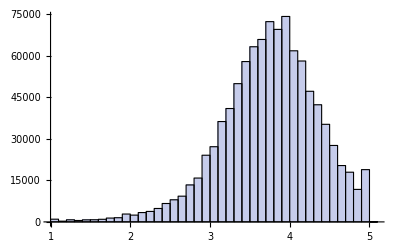

```mathematica
Histogram[Table[scorelist2[[i,2]],{i,1000000}],HistogramCategories->40]
```

```mathematica
Clear[Histogram]
```

```mathematica
scorelist2>>answer;
```

Do some experiments on the prediction quality of meanfieldscore versus knesset.  Find out the relative rms between them.

```mathematica
mftest=Table[meanfieldscore[pss2[[i,1]],pss2[[i,2]]],{i,Length[pss2]}];
```

```mathematica
Sum[If[scorelist[[i,2]]≠"Flub",(scorelist[[i,2]]-mftest[[i]])^2,0],{i,Length[pss2]}]
```

6613.68

They hang together pretty tightly.  Here's the rms:

```mathematica
Sqrt[6613.8/28858.]
```

0.478732

We can also run this experiement on the qualifying data.  It shouldn't be too different or something might be wrong.

```mathematica
Take[synqualsort2,10]
```

{{477,6},{1425,6},{1324,6},{1201,6},{1104,6},{1073,6},{6240,7},{14482,7},{13534,7},{11844,7}}

```mathematica
qualtest=Table[meanfieldscore[synqualeval[[i,1]],synqualeval[[i,2]]],{i,Length[synqualeval]}];
```

For some reason, Sum has a bug in it.  It won't sum over a million elements. So kludge an answer with Plus

```mathematica
Plus@@Table[If[bigscorelist[[i,2]]≠"Flub",(bigscorelist[[i,2]]-qualtest[[i]])^2,0],{i,1,Length[synqualsort2]}]
```

527951.

```mathematica
Sqrt[527951./Length[synqualsort2]]
```

0.432906

Nothing convincingly wrong.  If there were scrambling, this would be much higher.  The scrambling must be further on.

```mathematica
scorelist>>bigscorelist;
```

```mathematica
MemoryInUse[]
```

910414136

Find out where the algorithm "jumped the track".

```mathematica
synqualsort[[1925328]]
```

{12232,1808649}

It's a missing person!

```mathematica
reversepersontable[[1808649]]
```

0

Are there more?  Yes, six total.  Here are their positions in synqualsort.

```mathematica
missingpersonpositions=DeleteCases[Table[If[reversepersontable[[synqualsort[[i,2]]]]==0,i,0],{i,Length[synqualsort]}],0]
```

{151428,565322,1925328,2013934,2438542,2728770}

```mathematica
missingpersonnumbers=Table[synqualsort[[missingpersonpositions[[i]],2]],{i,Length[missingpersonpositions]}]
```

{142592,530204,1808649,1892856,2294145,2566440}

```mathematica
Table[reversepersontable[[missingpersonnumbers[[i]]]],{i,6}]
```

{0,0,0,0,0,0}

I'll just replace the person with the previous person in the sorted list so the scoring algorithm doesn't trip.

```mathematica
reversepersontable[[synqualsort[[151427,2]]]]
```

25875

Or, in general (first check for missing people, then for non missing neighbors on both sides, then synqualsort indices)

```mathematica
Table[synqualsort[[missingpersonpositions[[i]],2]],{i,6}]
Table[reversepersontable[[synqualsort[[missingpersonpositions[[i]],2]]]],{i,6}]
Table[reversepersontable[[synqualsort[[missingpersonpositions[[i]]-1,2]]]],{i,6}]
Table[reversepersontable[[synqualsort[[missingpersonpositions[[i]]+1,2]]]],{i,6}]
Table[synqualsort[[missingpersonpositions[[i]]-1,2]],{i,6}]
Table[synqualsort[[missingpersonpositions[[i]]+1,2]],{i,6}]
```

{142592,530204,1808649,1892856,2294145,2566440}

{0,0,0,0,0,0}

{25875,96403,328103,343231,415694,465136}

{25876,96404,328104,343232,415695,465137}

{142584,530203,1808648,1892852,2294135,2566439}

{142608,530211,1808651,1892862,2294165,2566443}

Now modify the synqualsort to assign "neighboring" real people to the ghost people and create synqualsort2.

```mathematica
synqualsort2=synqualsort;
```

```mathematica
Do[synqualsort2[[missingpersonpositions[[i]],2]]=synqualsort[[missingpersonpositions[[i]]-1,2]],{i,Length[missingpersonpositions]}]
```

Check to see if I got them all.  Hallelujah!

```mathematica
DeleteCases[Table[If[reversepersontable[[synqualsort2[[i,2]]]]==0,i,0],{i,Length[synqualsort2]}],0]
```

{}

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles"]
FileNames[]
```

/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles

{answer1.txt.gz,BulkStats,.DS_Store,finalform,matchscores,meanfieldexamscores,mfanswerclip2.txt.gz,mfanswerclip.txt,mfanswer.txt.gz,msfinal,PeopleByMovies,peopleids,peopleids2,probe,probescores,probesorted,probesortsample,pss2,synqual,synqualsort,synqualsort3,TestFolder,titles,TrainingMma}

```mathematica
synqualsort2>>synqualsort2;
```

Were there any missing persons in the probe set?  No.

```mathematica
DeleteCases[Table[If[reversepersontable[[probesorted[[i,2]]]]==0,i,0],{i,Length[probesorted]}],0]
```

{}

```mathematica
Take[synqualsort2,3]
```

{{477,6},{1425,6},{1324,6}}

```mathematica
synqualsort2[[2000000]]
```

{5515,1879485}

```mathematica
Position[synqualsort2,1879485]
```

{{1999998,2},{1999999,2},{2000000,2},{2000001,2},{2000002,2},{2000003,2}}

```mathematica
Take[synqualsort2,{1999997,2000004}]
```

{{14961,1879482},{8117,1879485},{6973,1879485},{5515,1879485},{14890,1879485},{12966,1879485},{11077,1879485},{6386,1879489}}

```mathematica
Take[synqualsort3,{1999997,2000004}]
```

{{14961,1879482,738303},{8117,1879485,2579063},{6973,1879485,2415354},{5515,1879485,2112233},{14890,1879485,725730},{12966,1879485,450386},{11077,1879485,154784},{6386,1879489,2307116}}

```mathematica
FileNames[]
```

{avgdist,avgdistpers,avgvector,avgvectorpers,citpts,citpts15,citpts4,citpts5,cumreviewplot,.DS_Store,fastknesset,fitmavens,grandaveragebyperson,grandaveragebyreview,mavenmatrix,mavenmoviematrix225,mavens,mavens225,meanmatrix,mrplot,personalmavs1,personalmavs10,personalmavs15,personalmavs5,personalmavslt5,personalstdev,plotrevbyscorebyperson,popplot,revbyscorebyperson,revbyscorebypersonfit,reviews,reviewspers,seculardrift,testfastknesset,thousandknesset,thousandmean,thousandvariance,variancematrix}

```mathematica
scorelist>>fulltestscorelist;
```

```mathematica
Sum[If[scorelist[[j,2]]≠"Flub", (scorelist[[j,1]]-Round[10 scorelist[[j,2]]]/10)^2,(meanfieldscore[probesorted[[j,1]],probesorted[[j,2]]]-probesorted[[j,3]])^2],{j,1000000,1400000}]
Clear[i];
```

280364.

```mathematica
Length[scorelist].
```

1408395

```mathematica
Sqrt[(286244.+697622.)/1408395]/.97
```

0.861656

```mathematica
MemoryInUse[]
```

980438928

```mathematica
Do[{getscores2[j],Print[Sum[If[scorelist[[i,2]]≠"Flub", (scorelist[[i,1]]-Round[10 scorelist[[i,2]]]/10)^2,(meanfieldscore[pss2[[i,1]],pss2[[i,2]]]-pss2[[i,3]])^2],{i,Length[scorelist]}]]
},{j,4,4}]
```

20008.1

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
ftk=OpenRead["fastknesset"];
knetable=Table[Read[ftk],{i,10000}];
Close[ftk];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/NetFlixPrize/NetFlixMmaFiles/BulkStats"];
ftk=OpenRead["fastknesset"];
Do[Read[ftk],{i,328102}];
knix=Table[Read[ftk],{j,3}];
Close[ftk];
```

```mathematica
Take[synqualsort,10]
```

{{477,6},{1425,6},{1324,6},{1201,6},{1104,6},{1073,6},{6240,7},{14482,7},{13534,7},{11844,7}}

How many different people are represented in the qualifying dataset?

```mathematica
Length[Union[Table[synqualsort[[i,2]],{i,Length[synqualsort]}]]]
```

478615

And how many different movies?

```mathematica
Length[Union[Table[synqualsort[[i,1]],{i,Length[synqualsort]}]]]
```

17470

How many people are represented in the probe set?

```mathematica
Length[Union[Table[probesorted[[i,2]],{i,Length[probesorted]}]]]
```

462795

And how many movies in the probe set?  It had better be 16 938, since that's what we started with.

```mathematica
Length[Union[Table[probesorted[[i,1]],{i,Length[probesorted]}]]]
```

16938